```mathematica
F[{x_, y_, z_}] := {4y-5z, 3y-4z};
```

```mathematica
Euler[F_, x0_, {y0_, z0_}, h_,xMax]:=Module[
{pts={{x0, y0, z0}}, x=x0, y=y0, z=z0, dy, dz},
While[x<xMax,
{dy, dz}=F[{x, y, z}];
y=y+h dy;
z= z+h dz;
x= x+h;
AppendTo[pts, {x, y, z}];
];
pts];
```

```mathematica
Runge[F_, x0_, {y0_, z0_}, h_,xMax]:=Module[
{pts={{x0, y0, z0}}, x=x0, y=y0, z=z0, k1, k2, k3, k4},
While[x<xMax,
k1=F[{x, y, z}];
k2 = F[x+h/2, y+h k1[[1]]/2, z+h k1[[2]]/2];
k3 = F[x+h/2, y+h k2[[1]]/2, z+h k2[[2]]/2];
k4 = F[x+h, y+h k3[[1]], z+h k3[[2]]];
y=y+(h/6)(k1[[1]]+2 k2[[1]]+2 k3[[1]]+k4[[1]]);
z=z+(h/6)(k1[[2]]+2 k2[[2]]+2 k3[[2]]+k4[[2]]);
x= x+h;
AppendTo[pts, {x, y, z}];
];
pts];
```

```mathematica
exact = DSolve[{y'[x]==4 y[x]-5 z[x], z'[x]==3y[x] - 4z[x], y[0]==2.5, z[0]==1}, {y, z}, x];
exactNum = NDSolveValue[{y'[x]==4 y[x]-5 z[x], z'[x]==3y[x] - 4z[x], y[0]==2.5, z[0]==1}, {y, z}, {x, 0, 1}];
```

```mathematica
e1 = Euler[F, 0, {2.5, 1}, 0.1, 1];
e2 = Euler[F, 0, {2.5, 1}, 0.05, 1];
r1 = Runge[F, 0, {2.5, 1}, 0.1, 1];
r2 = Runge[F, 0, {2.5, 1}, 0.05, 1];
```

```mathematica
Err[pts_, yf_, zf_] := Module[
{xs, ys, zs},
{xs, ys, zs} = Transpose[pts];
{
N[Mean[Abs[ys-yf /@ xs]]],
N[Mean[Abs[zs-zf /@ xs]]]
}];
```

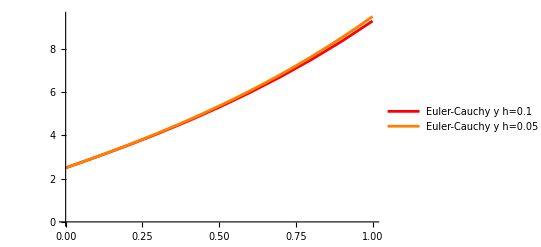

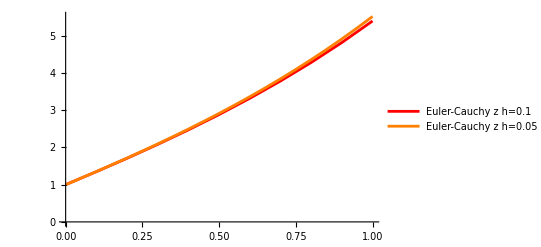

Error Euler-Cauchy h=0.1 (y, z): {0.162137,0.0905314}

Error Euler-Cauchy  h=0.05 (y, z): {0.0832044,0.0465842}

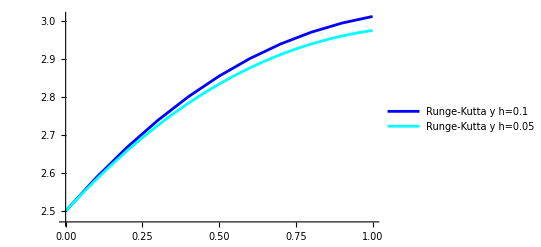

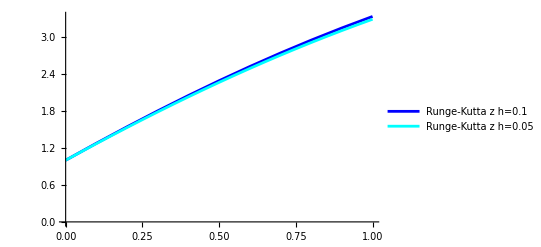

Error Runge-Kutta y h=0.1 (y, z): {2.88399,0.860599}

Error Runge-Kutta y h=0.05 (y, z): {2.87752,0.869316}

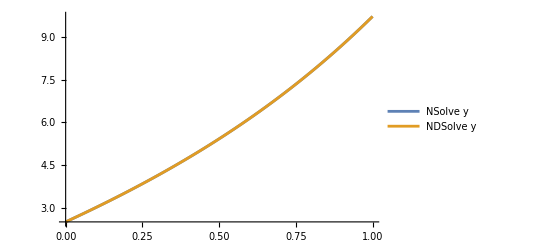

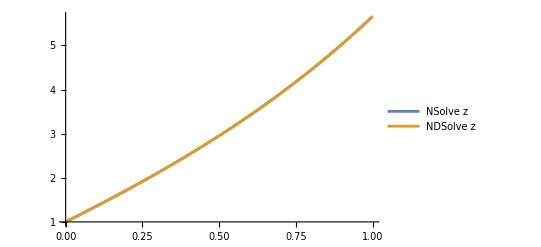

```mathematica
ListLinePlot[{e1[[All, {1, 2}]], e2[[All, {1, 2}]]}, PlotStyle->{Red, Orange}, PlotLegends->{"Euler-Cauchy y h=0.1", "Euler-Cauchy y h=0.05"}]

ListLinePlot[{e1[[All, {1, 3}]], e2[[All, {1, 3}]]}, PlotStyle->{Red, Orange}, PlotLegends->{"Euler-Cauchy z h=0.1", "Euler-Cauchy z h=0.05"}]
Print["Error Euler-Cauchy h=0.1 (y, z): ", Err[e1, exactNum[[1]], exactNum[[2]]]];
Print["Error Euler-Cauchy  h=0.05 (y, z): ", Err[e2, exactNum[[1]], exactNum[[2]]]];


ListLinePlot[{r1[[All, {1, 2}]], r2[[All, {1, 2}]]}, PlotStyle->{Blue, Cyan}, PlotLegends->{"Runge-Kutta y h=0.1", "Runge-Kutta y h=0.05"}]

ListLinePlot[{r1[[All, {1, 3}]], r2[[All, {1, 3}]]}, PlotStyle->{Blue, Cyan}, PlotLegends->{"Runge-Kutta z h=0.1", "Runge-Kutta z h=0.05"}]
Print["Error Runge-Kutta y h=0.1 (y, z): ", Err[r1, exactNum[[1]], exactNum[[2]]]];
Print["Error Runge-Kutta y h=0.05 (y, z): ", Err[r2, exactNum[[1]], exactNum[[2]]]];



Plot[{y[x] /. exact[[1]], exactNum[[1]][x]}, {x, 0, 1},
PlotLegends->{"NSolve y", "NDSolve y"}]
Plot[{z[x] /. exact[[1]], exactNum[[2]][x]}, {x, 0, 1},
PlotLegends->{"NSolve z", "NDSolve z"}]
```